```mathematica
comp1[x_] := 1.0*x/(1.0*x*1.0*Exp[1.0*x]*1.0*Exp[1.0*Sin[1.0*x+1.0]]+1.0*Exp[1.0*x]*1.0*Exp[1.0*Sin[1.0*x+1.0]])+1.0
comp2[x_] := 1.0*Sqrt[1.0*Abs[1.0*Sqrt[1.0*Abs[1.0*x+1.0]]]]*1.0*Sin[1.0*x/(1.0*x+1.0)+1.0/(1.0*x+1.0)]+1.0
comp3[x_] := 1.0*Sqrt[1.0*Abs[1.0*x/(1.0*x+1.0)+1.0/(1.0*x+1.0)]]+1.0*Sqrt[1.0*Abs[1.0*Exp[1.0*x]]]+1.0
comp4[x_] := 1.0*Sqrt[1.0*Abs[1.0*x]]+1.0/(x*1.0*Sqrt[1.0*Abs[1.0*x]]*1.0*Sqrt[1.0*Abs[1.0*x]])+1.0
comp5[x_] := 1.0*x/(1.0*x*1.0*Sqrt[1.0*Abs[1.0*Log[1.0*x]]]+1.0*Sqrt[1.0*Abs[1.0*Log[1.0*x]]])+1.0
comp6[x_] := 1.0*x^2*1.0*Sqrt[1.0*Abs[1.0*x+1.0]]+1.0*x+1.0*x/(1.0*x)+1.0*Log[1.0*x+1.0]+1.0
comp7[x_] := 1.0*Sqrt[1.0*Abs[1.0*x*1.0*Sqrt[1.0*Abs[1.0*x]]/(1.0*x+1.0)+1.0/(1.0*x+1.0)]]+1.0
comp8[x_] := 1.0*x^2+1.0*x+1.0*Exp[1.0*x]/1.0*Sqrt[1.0*Abs[1.0*Sqrt[1.0*Abs[1.0*x+1.0]]]]+1.0
myEqns = {comp1, comp2, comp3, comp4, comp5, comp6, comp7, comp8};
```

```mathematica
Print["Complicated Benchmark Equations"]
Do[Print[Simplify[eqn[x]]," evaluated at 0.1 = ", N[eqn[.1]]];,
 {eqn, myEqns
}]
```

1.+1. x+1. x^2+1. ⅇ^(1. x) Abs[1.+1. x]^(1/4) evaluated at 0.1 = 2.24182

1.+1. √Abs[(1.+1. x √Abs[x])/(1.+1. x)] evaluated at 0.1 = 1.96842

2.+1. x+1. x^2 √Abs[1.+1. x]+1. Log[1.+1. x] evaluated at 0.1 = 2.2058

1.+(1. x)/((1.+1. x) √Abs[0.+Log[x]]) evaluated at 0.1 = 1.05991

1.+1./(x Abs[x])+1. √Abs[x] evaluated at 0.1 = 101.316

2.+1. ⅇ^(0.5 Re[x]) evaluated at 0.1 = 3.05127

1.+0.841471 Abs[1.+1. x]^(1/4) evaluated at 0.1 = 1.86176

1.+(1. ⅇ^(-1. x-1. Sin[1.+1. x]) x)/(1.+1. x) evaluated at 0.1 = 1.03374

Complicated Benchmark Equations

1.+1. x+1. x^2+1. ⅇ^(1. x) Abs[1.+1. x]^(1/4) evaluated at 0.1 = 2.24182

1.+1. √Abs[(1.+1. x √Abs[x])/(1.+1. x)] evaluated at 0.1 = 1.96842

2.+1. x+1. x^2 √Abs[1.+1. x]+1. Log[1.+1. x] evaluated at 0.1 = 2.2058

1.+(1. x)/((1.+1. x) √Abs[0.+Log[x]]) evaluated at 0.1 = 1.05991

1.+1./(x Abs[x])+1. √Abs[x] evaluated at 0.1 = 101.316

2.+1. ⅇ^(0.5 Re[x]) evaluated at 0.1 = 3.05127

1.+0.841471 Abs[1.+1. x]^(1/4) evaluated at 0.1 = 1.86176

1.+(1. ⅇ^(-1. x-1. Sin[1.+1. x]) x)/(1.+1. x) evaluated at 0.1 = 1.03374

Complicated Benchmark Equations

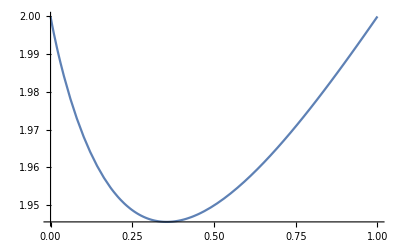

```mathematica
Plot[comp7[x], {x,0,1}]
```

```mathematica
|
```

```mathematica
rangeMin = 0.0;
rangeMax = 1.0;
numberSamples = 20;
numberTrials = 100;
Do[
evals  = {};
mses = {};
For[ii=1, ii<=numberTrials, ii++,
SeedRandom[ii];
myX = RandomReal[{rangeMin,rangeMax},{numberSamples}];
y = eqn[myX];

predFn = FindFormula[Transpose[{myX,y}],x,1, "Error"];
isCorrect =If[Simplify[Expand[eqn[x]]] ==Simplify[Part[predFn,1]],1,0,0];
myMSE = Part[predFn,2];
evals = Append[evals, isCorrect];
mses = Append[mses, myMSE];
];
Print[Simplify[eqn[x]]];
Print["Mean recovery = ", N[Mean[evals],4]];
Print["Mean MSE = ", N[Mean[mses],3]," +/- ", N[StandardDeviation[mses],3], "standard deviation"];,
{eqn, myEqns}
]
Print["\n Finished"];
```

1.+(1. ⅇ^(-1. x-1. Sin[1.+1. x]) x)/(1.+1. x)

Mean recovery = 0

Mean MSE = 5.7167×10^-17

+/- MSE Standard Deviation = 7.82539×10^-17

1.+1./(x Abs[x])+1. √Abs[x]

Mean recovery = 0

Mean MSE = 694.281

+/- MSE Standard Deviation = 2004.73

1.+(1. x)/((1.+1. x) √Abs[0.+Log[x]])

Mean recovery = 0

Mean MSE = 0.480478

+/- MSE Standard Deviation = 1.0792

2.+1. x+1. x^2 √Abs[1.+1. x]+1. Log[1.+1. x]

Mean recovery = 0

Mean MSE = 1.48417×10^-18

+/- MSE Standard Deviation = 1.39988×10^-18

1.+1. √Abs[(1.+1. x √Abs[x])/(1.+1. x)]

Mean recovery = 0

Mean MSE = 0.00015597

+/- MSE Standard Deviation = 0.000135972

1.+1. x+1. x^2+1. ⅇ^(1. x) Abs[1.+1. x]^(1/4)

Mean recovery = 0

Mean MSE = 1.44194×10^-19

+/- MSE Standard Deviation = 1.34354×10^-19

Finished